NDSolve::ndsz: At x == 0.532797, step size is effectively zero; singularity or stiff system suspected.

--- TOV Solver Results ---

Dimensionless Radius (R/R0): 0.532797

Dimensionless Mass (M/mu): 0.0690837

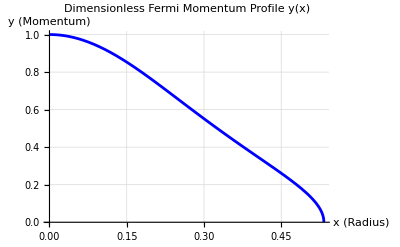

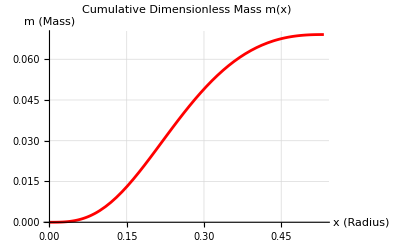

```mathematica
(*1. Define the integrand functions for f(y) and g(y)*)fIntegrand[t_]:=t^4/Sqrt[t^2+1];
gIntegrand[t_]:=t^2*Sqrt[t^2+1];

(*2. Set the central dimensionless Fermi momentum (yc)*)
(*This parameter controls the central density of the neutron star*)
yc=1.0;

(*3. Define the system of Coupled Differential Equations*)
(*We treat fVal and gVal as functions of x to avoid re-integrating at every step*)
tovEquations={y'[x]==-((m[x]+4*Pi*x^3*fVal[x])*(3*gVal[x]+fVal[x]))/(x*(x-2*m[x])*(y[x]^4/Sqrt[y[x]^2+1])),m'[x]==12*Pi*x^2*gVal[x],fVal'[x]==fIntegrand[y[x]]*y'[x],gVal'[x]==gIntegrand[y[x]]*y'[x]};

(*4. Set Initial Conditions (near the origin x=0)*)
(*We use a small epsilon offset to avoid the numerical singularity at x=0*)
epsilon=10^-8;
initialConditions={y[epsilon]==yc,m[epsilon]==0,fVal[epsilon]==NIntegrate[fIntegrand[t],{t,0,yc}],gVal[epsilon]==NIntegrate[gIntegrand[t],{t,0,yc}]};

(*5. Solve using NDSolve*)
(*We use "EventLocator" to stop integration when y(x) hits 0 (the star surface)*)
solution=NDSolve[Join[tovEquations,initialConditions],{y,m,fVal,gVal},{x,epsilon,10},Method->{"EventLocator","Event"->y[x],"Direction"->-1}];

(*6. Extract Results:Surface Radius and Total Mass*)
xSurface=(y/. solution[[1]])["Domain"][[1,2]];
mTotal=(m/. solution[[1]])[xSurface];

Print["--- TOV Solver Results ---"];
Print["Dimensionless Radius (R/R0): ",xSurface];
Print["Dimensionless Mass (M/mu): ",mTotal];

(*7. Plotting the Profiles*)
Plot[Evaluate[y[x]/. solution],{x,epsilon,xSurface},PlotLabel->"Dimensionless Fermi Momentum Profile y(x)",AxesLabel->{"x (Radius)","y (Momentum)"},PlotStyle->Blue,GridLines->Automatic]

Plot[Evaluate[m[x]/. solution],{x,epsilon,xSurface},PlotLabel->"Cumulative Dimensionless Mass m(x)",AxesLabel->{"x (Radius)","m (Mass)"},PlotStyle->Red,GridLines->Automatic]
```

Calculating M-R Data Points...

Computing yc = 0.01

Computing yc = 0.011

Computing yc = 0.012

Computing yc = 0.013

Computing yc = 0.014

Computing yc = 0.015

Computing yc = 0.016

Computing yc = 0.017

Computing yc = 0.018

Computing yc = 0.019

Computing yc = 0.02

Computing yc = 0.021

Computing yc = 0.022

Computing yc = 0.023

Computing yc = 0.024

Computing yc = 0.025

Computing yc = 0.026

Computing yc = 0.027

Computing yc = 0.028

Computing yc = 0.029

Computing yc = 0.03

Computing yc = 0.031

Computing yc = 0.032

Computing yc = 0.033

Computing yc = 0.034

Computing yc = 0.035

Computing yc = 0.036

Computing yc = 0.037

Computing yc = 0.038

Computing yc = 0.039

Computing yc = 0.04

Computing yc = 0.041

Computing yc = 0.042

Computing yc = 0.043

Computing yc = 0.044

Computing yc = 0.045

Computing yc = 0.046

Computing yc = 0.047

Computing yc = 0.048

Computing yc = 0.049

Computing yc = 0.05

Computing yc = 0.051

Computing yc = 0.052

Computing yc = 0.053

Computing yc = 0.054

Computing yc = 0.055

Computing yc = 0.056

Computing yc = 0.057

Computing yc = 0.058

Computing yc = 0.059

Computing yc = 0.06

Computing yc = 0.061

Computing yc = 0.062

Computing yc = 0.063

Computing yc = 0.064

Computing yc = 0.065

Computing yc = 0.066

Computing yc = 0.067

Computing yc = 0.068

Computing yc = 0.069

Computing yc = 0.07

Computing yc = 0.071

Computing yc = 0.072

Computing yc = 0.073

Computing yc = 0.074

Computing yc = 0.075

Computing yc = 0.076

Computing yc = 0.077

Computing yc = 0.078

Computing yc = 0.079

Computing yc = 0.08

Computing yc = 0.081

Computing yc = 0.082

Computing yc = 0.083

Computing yc = 0.084

Computing yc = 0.085

Computing yc = 0.086

Computing yc = 0.087

Computing yc = 0.088

Computing yc = 0.089

Computing yc = 0.09

Computing yc = 0.091

Computing yc = 0.092

Computing yc = 0.093

Computing yc = 0.094

Computing yc = 0.095

Computing yc = 0.096

Computing yc = 0.097

Computing yc = 0.098

Computing yc = 0.099

Computing yc = 0.1

Computing yc = 0.101

Computing yc = 0.102

Computing yc = 0.103

Computing yc = 0.104

Computing yc = 0.105

Computing yc = 0.106

Computing yc = 0.107

Computing yc = 0.108

Computing yc = 0.109

Computing yc = 0.11

Computing yc = 0.111

Computing yc = 0.112

Computing yc = 0.113

Computing yc = 0.114

Computing yc = 0.115

Computing yc = 0.116

Computing yc = 0.117

Computing yc = 0.118

Computing yc = 0.119

Computing yc = 0.12

Computing yc = 0.121

Computing yc = 0.122

Computing yc = 0.123

Computing yc = 0.124

Computing yc = 0.125

Computing yc = 0.126

Computing yc = 0.127

Computing yc = 0.128

Computing yc = 0.129

Computing yc = 0.13

Computing yc = 0.131

Computing yc = 0.132

Computing yc = 0.133

Computing yc = 0.134

Computing yc = 0.135

Computing yc = 0.136

Computing yc = 0.137

Computing yc = 0.138

Computing yc = 0.139

Computing yc = 0.14

Computing yc = 0.141

Computing yc = 0.142

Computing yc = 0.143

Computing yc = 0.144

Computing yc = 0.145

Computing yc = 0.146

Computing yc = 0.147

Computing yc = 0.148

Computing yc = 0.149

Computing yc = 0.15

Computing yc = 0.151

Computing yc = 0.152

Computing yc = 0.153

Computing yc = 0.154

Computing yc = 0.155

Computing yc = 0.156

Computing yc = 0.157

Computing yc = 0.158

Computing yc = 0.159

Computing yc = 0.16

Computing yc = 0.161

Computing yc = 0.162

Computing yc = 0.163

Computing yc = 0.164

Computing yc = 0.165

Computing yc = 0.166

Computing yc = 0.167

Computing yc = 0.168

Computing yc = 0.169

Computing yc = 0.17

Computing yc = 0.171

Computing yc = 0.172

Computing yc = 0.173

Computing yc = 0.174

Computing yc = 0.175

Computing yc = 0.176

Computing yc = 0.177

Computing yc = 0.178

Computing yc = 0.179

Computing yc = 0.18

Computing yc = 0.181

Computing yc = 0.182

Computing yc = 0.183

Computing yc = 0.184

Computing yc = 0.185

Computing yc = 0.186

Computing yc = 0.187

Computing yc = 0.188

Computing yc = 0.189

Computing yc = 0.19

Computing yc = 0.191

Computing yc = 0.192

Computing yc = 0.193

Computing yc = 0.194

Computing yc = 0.195

Computing yc = 0.196

Computing yc = 0.197

Computing yc = 0.198

Computing yc = 0.199

Computing yc = 0.2

Computing yc = 0.201

Computing yc = 0.202

Computing yc = 0.203

Computing yc = 0.204

Computing yc = 0.205

Computing yc = 0.206

Computing yc = 0.207

Computing yc = 0.208

Computing yc = 0.209

Computing yc = 0.21

Computing yc = 0.211

Computing yc = 0.212

Computing yc = 0.213

Computing yc = 0.214

Computing yc = 0.215

Computing yc = 0.216

Computing yc = 0.217

Computing yc = 0.218

Computing yc = 0.219

Computing yc = 0.22

Computing yc = 0.221

Computing yc = 0.222

Computing yc = 0.223

Computing yc = 0.224

Computing yc = 0.225

Computing yc = 0.226

Computing yc = 0.227

Computing yc = 0.228

Computing yc = 0.229

Computing yc = 0.23

Computing yc = 0.231

Computing yc = 0.232

Computing yc = 0.233

Computing yc = 0.234

Computing yc = 0.235

Computing yc = 0.236

Computing yc = 0.237

Computing yc = 0.238

Computing yc = 0.239

Computing yc = 0.24

Computing yc = 0.241

Computing yc = 0.242

Computing yc = 0.243

Computing yc = 0.244

Computing yc = 0.245

Computing yc = 0.246

Computing yc = 0.247

Computing yc = 0.248

Computing yc = 0.249

Computing yc = 0.25

Computing yc = 0.251

Computing yc = 0.252

Computing yc = 0.253

Computing yc = 0.254

Computing yc = 0.255

Computing yc = 0.256

Computing yc = 0.257

Computing yc = 0.258

Computing yc = 0.259

Computing yc = 0.26

Computing yc = 0.261

Computing yc = 0.262

Computing yc = 0.263

Computing yc = 0.264

Computing yc = 0.265

Computing yc = 0.266

Computing yc = 0.267

Computing yc = 0.268

Computing yc = 0.269

Computing yc = 0.27

Computing yc = 0.271

Computing yc = 0.272

Computing yc = 0.273

Computing yc = 0.274

Computing yc = 0.275

Computing yc = 0.276

Computing yc = 0.277

Computing yc = 0.278

Computing yc = 0.279

Computing yc = 0.28

Computing yc = 0.281

Computing yc = 0.282

Computing yc = 0.283

Computing yc = 0.284

Computing yc = 0.285

Computing yc = 0.286

Computing yc = 0.287

Computing yc = 0.288

Computing yc = 0.289

Computing yc = 0.29

Computing yc = 0.291

Computing yc = 0.292

Computing yc = 0.293

Computing yc = 0.294

Computing yc = 0.295

Computing yc = 0.296

Computing yc = 0.297

Computing yc = 0.298

Computing yc = 0.299

Computing yc = 0.3

Computing yc = 0.301

Computing yc = 0.302

Computing yc = 0.303

Computing yc = 0.304

Computing yc = 0.305

Computing yc = 0.306

Computing yc = 0.307

Computing yc = 0.308

Computing yc = 0.309

Computing yc = 0.31

Computing yc = 0.311

Computing yc = 0.312

Computing yc = 0.313

Computing yc = 0.314

Computing yc = 0.315

Computing yc = 0.316

Computing yc = 0.317

Computing yc = 0.318

Computing yc = 0.319

Computing yc = 0.32

Computing yc = 0.321

Computing yc = 0.322

Computing yc = 0.323

Computing yc = 0.324

Computing yc = 0.325

Computing yc = 0.326

Computing yc = 0.327

Computing yc = 0.328

Computing yc = 0.329

Computing yc = 0.33

Computing yc = 0.331

Computing yc = 0.332

Computing yc = 0.333

Computing yc = 0.334

Computing yc = 0.335

Computing yc = 0.336

Computing yc = 0.337

Computing yc = 0.338

Computing yc = 0.339

Computing yc = 0.34

Computing yc = 0.341

Computing yc = 0.342

Computing yc = 0.343

Computing yc = 0.344

Computing yc = 0.345

Computing yc = 0.346

Computing yc = 0.347

Computing yc = 0.348

Computing yc = 0.349

Computing yc = 0.35

Computing yc = 0.351

Computing yc = 0.352

Computing yc = 0.353

Computing yc = 0.354

Computing yc = 0.355

Computing yc = 0.356

Computing yc = 0.357

Computing yc = 0.358

Computing yc = 0.359

Computing yc = 0.36

Computing yc = 0.361

Computing yc = 0.362

Computing yc = 0.363

Computing yc = 0.364

Computing yc = 0.365

Computing yc = 0.366

Computing yc = 0.367

Computing yc = 0.368

Computing yc = 0.369

Computing yc = 0.37

Computing yc = 0.371

Computing yc = 0.372

Computing yc = 0.373

Computing yc = 0.374

Computing yc = 0.375

Computing yc = 0.376

Computing yc = 0.377

Computing yc = 0.378

Computing yc = 0.379

Computing yc = 0.38

Computing yc = 0.381

Computing yc = 0.382

Computing yc = 0.383

Computing yc = 0.384

Computing yc = 0.385

Computing yc = 0.386

Computing yc = 0.387

Computing yc = 0.388

Computing yc = 0.389

Computing yc = 0.39

Computing yc = 0.391

Computing yc = 0.392

Computing yc = 0.393

Computing yc = 0.394

Computing yc = 0.395

Computing yc = 0.396

Computing yc = 0.397

Computing yc = 0.398

Computing yc = 0.399

Computing yc = 0.4

Computing yc = 0.401

Computing yc = 0.402

Computing yc = 0.403

Computing yc = 0.404

Computing yc = 0.405

Computing yc = 0.406

Computing yc = 0.407

Computing yc = 0.408

Computing yc = 0.409

Computing yc = 0.41

Computing yc = 0.411

Computing yc = 0.412

Computing yc = 0.413

Computing yc = 0.414

Computing yc = 0.415

Computing yc = 0.416

Computing yc = 0.417

Computing yc = 0.418

Computing yc = 0.419

Computing yc = 0.42

Computing yc = 0.421

Computing yc = 0.422

Computing yc = 0.423

Computing yc = 0.424

Computing yc = 0.425

Computing yc = 0.426

Computing yc = 0.427

Computing yc = 0.428

Computing yc = 0.429

Computing yc = 0.43

Computing yc = 0.431

Computing yc = 0.432

Computing yc = 0.433

Computing yc = 0.434

Computing yc = 0.435

Computing yc = 0.436

Computing yc = 0.437

Computing yc = 0.438

Computing yc = 0.439

Computing yc = 0.44

Computing yc = 0.441

Computing yc = 0.442

Computing yc = 0.443

Computing yc = 0.444

Computing yc = 0.445

Computing yc = 0.446

Computing yc = 0.447

Computing yc = 0.448

Computing yc = 0.449

Computing yc = 0.45

Computing yc = 0.451

Computing yc = 0.452

Computing yc = 0.453

Computing yc = 0.454

Computing yc = 0.455

Computing yc = 0.456

Computing yc = 0.457

Computing yc = 0.458

Computing yc = 0.459

Computing yc = 0.46

Computing yc = 0.461

Computing yc = 0.462

Computing yc = 0.463

Computing yc = 0.464

Computing yc = 0.465

Computing yc = 0.466

Computing yc = 0.467

Computing yc = 0.468

Computing yc = 0.469

Computing yc = 0.47

Computing yc = 0.471

Computing yc = 0.472

Computing yc = 0.473

Computing yc = 0.474

Computing yc = 0.475

Computing yc = 0.476

Computing yc = 0.477

Computing yc = 0.478

Computing yc = 0.479

Computing yc = 0.48

Computing yc = 0.481

Computing yc = 0.482

Computing yc = 0.483

Computing yc = 0.484

Computing yc = 0.485

Computing yc = 0.486

Computing yc = 0.487

Computing yc = 0.488

Computing yc = 0.489

Computing yc = 0.49

Computing yc = 0.491

Computing yc = 0.492

Computing yc = 0.493

Computing yc = 0.494

Computing yc = 0.495

Computing yc = 0.496

Computing yc = 0.497

Computing yc = 0.498

Computing yc = 0.499

Computing yc = 0.5

Computing yc = 0.501

Computing yc = 0.502

Computing yc = 0.503

Computing yc = 0.504

Computing yc = 0.505

Computing yc = 0.506

Computing yc = 0.507

Computing yc = 0.508

Computing yc = 0.509

Computing yc = 0.51

Computing yc = 0.511

Computing yc = 0.512

Computing yc = 0.513

Computing yc = 0.514

Computing yc = 0.515

Computing yc = 0.516

Computing yc = 0.517

Computing yc = 0.518

Computing yc = 0.519

Computing yc = 0.52

Computing yc = 0.521

Computing yc = 0.522

Computing yc = 0.523

Computing yc = 0.524

Computing yc = 0.525

Computing yc = 0.526

Computing yc = 0.527

Computing yc = 0.528

Computing yc = 0.529

Computing yc = 0.53

Computing yc = 0.531

Computing yc = 0.532

Computing yc = 0.533

Computing yc = 0.534

Computing yc = 0.535

Computing yc = 0.536

Computing yc = 0.537

Computing yc = 0.538

Computing yc = 0.539

Computing yc = 0.54

Computing yc = 0.541

Computing yc = 0.542

Computing yc = 0.543

Computing yc = 0.544

Computing yc = 0.545

Computing yc = 0.546

Computing yc = 0.547

Computing yc = 0.548

Computing yc = 0.549

Computing yc = 0.55

Computing yc = 0.551

Computing yc = 0.552

Computing yc = 0.553

Computing yc = 0.554

Computing yc = 0.555

Computing yc = 0.556

Computing yc = 0.557

Computing yc = 0.558

Computing yc = 0.559

Computing yc = 0.56

Computing yc = 0.561

Computing yc = 0.562

Computing yc = 0.563

Computing yc = 0.564

Computing yc = 0.565

Computing yc = 0.566

Computing yc = 0.567

Computing yc = 0.568

Computing yc = 0.569

Computing yc = 0.57

Computing yc = 0.571

Computing yc = 0.572

Computing yc = 0.573

Computing yc = 0.574

Computing yc = 0.575

Computing yc = 0.576

Computing yc = 0.577

Computing yc = 0.578

Computing yc = 0.579

Computing yc = 0.58

Computing yc = 0.581

Computing yc = 0.582

Computing yc = 0.583

Computing yc = 0.584

Computing yc = 0.585

Computing yc = 0.586

Computing yc = 0.587

Computing yc = 0.588

Computing yc = 0.589

Computing yc = 0.59

Computing yc = 0.591

Computing yc = 0.592

Computing yc = 0.593

Computing yc = 0.594

Computing yc = 0.595

Computing yc = 0.596

Computing yc = 0.597

Computing yc = 0.598

Computing yc = 0.599

Computing yc = 0.6

Computing yc = 0.601

Computing yc = 0.602

Computing yc = 0.603

Computing yc = 0.604

Computing yc = 0.605

Computing yc = 0.606

Computing yc = 0.607

Computing yc = 0.608

Computing yc = 0.609

Computing yc = 0.61

Computing yc = 0.611

Computing yc = 0.612

Computing yc = 0.613

Computing yc = 0.614

Computing yc = 0.615

Computing yc = 0.616

Computing yc = 0.617

Computing yc = 0.618

Computing yc = 0.619

Computing yc = 0.62

Computing yc = 0.621

Computing yc = 0.622

Computing yc = 0.623

Computing yc = 0.624

Computing yc = 0.625

Computing yc = 0.626

Computing yc = 0.627

Computing yc = 0.628

Computing yc = 0.629

Computing yc = 0.63

Computing yc = 0.631

Computing yc = 0.632

Computing yc = 0.633

Computing yc = 0.634

Computing yc = 0.635

Computing yc = 0.636

Computing yc = 0.637

Computing yc = 0.638

Computing yc = 0.639

Computing yc = 0.64

Computing yc = 0.641

Computing yc = 0.642

Computing yc = 0.643

Computing yc = 0.644

Computing yc = 0.645

Computing yc = 0.646

Computing yc = 0.647

Computing yc = 0.648

Computing yc = 0.649

Computing yc = 0.65

Computing yc = 0.651

Computing yc = 0.652

Computing yc = 0.653

Computing yc = 0.654

Computing yc = 0.655

Computing yc = 0.656

Computing yc = 0.657

Computing yc = 0.658

Computing yc = 0.659

Computing yc = 0.66

Computing yc = 0.661

Computing yc = 0.662

Computing yc = 0.663

Computing yc = 0.664

Computing yc = 0.665

Computing yc = 0.666

Computing yc = 0.667

Computing yc = 0.668

Computing yc = 0.669

Computing yc = 0.67

Computing yc = 0.671

Computing yc = 0.672

Computing yc = 0.673

Computing yc = 0.674

Computing yc = 0.675

Computing yc = 0.676

Computing yc = 0.677

Computing yc = 0.678

Computing yc = 0.679

Computing yc = 0.68

Computing yc = 0.681

Computing yc = 0.682

Computing yc = 0.683

Computing yc = 0.684

Computing yc = 0.685

Computing yc = 0.686

Computing yc = 0.687

Computing yc = 0.688

Computing yc = 0.689

Computing yc = 0.69

Computing yc = 0.691

Computing yc = 0.692

Computing yc = 0.693

Computing yc = 0.694

Computing yc = 0.695

Computing yc = 0.696

Computing yc = 0.697

Computing yc = 0.698

Computing yc = 0.699

Computing yc = 0.7

Computing yc = 0.701

Computing yc = 0.702

Computing yc = 0.703

Computing yc = 0.704

Computing yc = 0.705

Computing yc = 0.706

Computing yc = 0.707

Computing yc = 0.708

Computing yc = 0.709

Computing yc = 0.71

Computing yc = 0.711

Computing yc = 0.712

Computing yc = 0.713

Computing yc = 0.714

Computing yc = 0.715

Computing yc = 0.716

Computing yc = 0.717

Computing yc = 0.718

Computing yc = 0.719

Computing yc = 0.72

Computing yc = 0.721

Computing yc = 0.722

Computing yc = 0.723

Computing yc = 0.724

Computing yc = 0.725

Computing yc = 0.726

Computing yc = 0.727

Computing yc = 0.728

Computing yc = 0.729

Computing yc = 0.73

Computing yc = 0.731

Computing yc = 0.732

Computing yc = 0.733

Computing yc = 0.734

Computing yc = 0.735

Computing yc = 0.736

Computing yc = 0.737

Computing yc = 0.738

Computing yc = 0.739

Computing yc = 0.74

Computing yc = 0.741

Computing yc = 0.742

Computing yc = 0.743

Computing yc = 0.744

Computing yc = 0.745

Computing yc = 0.746

Computing yc = 0.747

Computing yc = 0.748

Computing yc = 0.749

Computing yc = 0.75

Computing yc = 0.751

Computing yc = 0.752

Computing yc = 0.753

Computing yc = 0.754

Computing yc = 0.755

Computing yc = 0.756

Computing yc = 0.757

Computing yc = 0.758

Computing yc = 0.759

Computing yc = 0.76

Computing yc = 0.761

Computing yc = 0.762

Computing yc = 0.763

Computing yc = 0.764

Computing yc = 0.765

Computing yc = 0.766

Computing yc = 0.767

Computing yc = 0.768

Computing yc = 0.769

Computing yc = 0.77

Computing yc = 0.771

Computing yc = 0.772

Computing yc = 0.773

Computing yc = 0.774

Computing yc = 0.775

Computing yc = 0.776

Computing yc = 0.777

Computing yc = 0.778

Computing yc = 0.779

Computing yc = 0.78

Computing yc = 0.781

Computing yc = 0.782

Computing yc = 0.783

Computing yc = 0.784

Computing yc = 0.785

Computing yc = 0.786

Computing yc = 0.787

Computing yc = 0.788

Computing yc = 0.789

Computing yc = 0.79

Computing yc = 0.791

Computing yc = 0.792

Computing yc = 0.793

Computing yc = 0.794

Computing yc = 0.795

Computing yc = 0.796

Computing yc = 0.797

Computing yc = 0.798

Computing yc = 0.799

Computing yc = 0.8

Computing yc = 0.801

Computing yc = 0.802

Computing yc = 0.803

Computing yc = 0.804

Computing yc = 0.805

Computing yc = 0.806

Computing yc = 0.807

Computing yc = 0.808

Computing yc = 0.809

Computing yc = 0.81

Computing yc = 0.811

Computing yc = 0.812

Computing yc = 0.813

Computing yc = 0.814

Computing yc = 0.815

Computing yc = 0.816

Computing yc = 0.817

Computing yc = 0.818

Computing yc = 0.819

Computing yc = 0.82

Computing yc = 0.821

Computing yc = 0.822

Computing yc = 0.823

Computing yc = 0.824

Computing yc = 0.825

Computing yc = 0.826

Computing yc = 0.827

Computing yc = 0.828

Computing yc = 0.829

Computing yc = 0.83

Computing yc = 0.831

Computing yc = 0.832

Computing yc = 0.833

Computing yc = 0.834

Computing yc = 0.835

Computing yc = 0.836

Computing yc = 0.837

Computing yc = 0.838

Computing yc = 0.839

Computing yc = 0.84

Computing yc = 0.841

Computing yc = 0.842

Computing yc = 0.843

Computing yc = 0.844

Computing yc = 0.845

Computing yc = 0.846

Computing yc = 0.847

Computing yc = 0.848

Computing yc = 0.849

Computing yc = 0.85

Computing yc = 0.851

Computing yc = 0.852

Computing yc = 0.853

Computing yc = 0.854

Computing yc = 0.855

Computing yc = 0.856

Computing yc = 0.857

Computing yc = 0.858

Computing yc = 0.859

Computing yc = 0.86

Computing yc = 0.861

Computing yc = 0.862

Computing yc = 0.863

Computing yc = 0.864

Computing yc = 0.865

Computing yc = 0.866

Computing yc = 0.867

Computing yc = 0.868

Computing yc = 0.869

Computing yc = 0.87

Computing yc = 0.871

Computing yc = 0.872

Computing yc = 0.873

Computing yc = 0.874

Computing yc = 0.875

Computing yc = 0.876

Computing yc = 0.877

Computing yc = 0.878

Computing yc = 0.879

Computing yc = 0.88

Computing yc = 0.881

Computing yc = 0.882

Computing yc = 0.883

Computing yc = 0.884

Computing yc = 0.885

Computing yc = 0.886

Computing yc = 0.887

Computing yc = 0.888

Computing yc = 0.889

Computing yc = 0.89

Computing yc = 0.891

Computing yc = 0.892

Computing yc = 0.893

Computing yc = 0.894

Computing yc = 0.895

Computing yc = 0.896

Computing yc = 0.897

Computing yc = 0.898

Computing yc = 0.899

Computing yc = 0.9

Computing yc = 0.901

Computing yc = 0.902

Computing yc = 0.903

Computing yc = 0.904

Computing yc = 0.905

Computing yc = 0.906

Computing yc = 0.907

Computing yc = 0.908

Computing yc = 0.909

Computing yc = 0.91

Computing yc = 0.911

Computing yc = 0.912

Computing yc = 0.913

Computing yc = 0.914

Computing yc = 0.915

Computing yc = 0.916

Computing yc = 0.917

Computing yc = 0.918

Computing yc = 0.919

Computing yc = 0.92

Computing yc = 0.921

Computing yc = 0.922

Computing yc = 0.923

Computing yc = 0.924

Computing yc = 0.925

Computing yc = 0.926

Computing yc = 0.927

Computing yc = 0.928

Computing yc = 0.929

Computing yc = 0.93

Computing yc = 0.931

Computing yc = 0.932

Computing yc = 0.933

Computing yc = 0.934

Computing yc = 0.935

Computing yc = 0.936

Computing yc = 0.937

Computing yc = 0.938

Computing yc = 0.939

Computing yc = 0.94

Computing yc = 0.941

Computing yc = 0.942

Computing yc = 0.943

Computing yc = 0.944

Computing yc = 0.945

Computing yc = 0.946

Computing yc = 0.947

Computing yc = 0.948

Computing yc = 0.949

Computing yc = 0.95

Computing yc = 0.951

Computing yc = 0.952

Computing yc = 0.953

Computing yc = 0.954

Computing yc = 0.955

Computing yc = 0.956

Computing yc = 0.957

Computing yc = 0.958

Computing yc = 0.959

Computing yc = 0.96

Computing yc = 0.961

Computing yc = 0.962

Computing yc = 0.963

Computing yc = 0.964

Computing yc = 0.965

Computing yc = 0.966

Computing yc = 0.967

Computing yc = 0.968

Computing yc = 0.969

Computing yc = 0.97

Computing yc = 0.971

Computing yc = 0.972

Computing yc = 0.973

Computing yc = 0.974

Computing yc = 0.975

Computing yc = 0.976

Computing yc = 0.977

Computing yc = 0.978

Computing yc = 0.979

Computing yc = 0.98

Computing yc = 0.981

Computing yc = 0.982

Computing yc = 0.983

Computing yc = 0.984

Computing yc = 0.985

Computing yc = 0.986

Computing yc = 0.987

Computing yc = 0.988

Computing yc = 0.989

Computing yc = 0.99

Computing yc = 0.991

Computing yc = 0.992

Computing yc = 0.993

Computing yc = 0.994

Computing yc = 0.995

Computing yc = 0.996

Computing yc = 0.997

Computing yc = 0.998

Computing yc = 0.999

Computing yc = 1.

Computing yc = 1.001

Computing yc = 1.002

Computing yc = 1.003

Computing yc = 1.004

Computing yc = 1.005

Computing yc = 1.006

Computing yc = 1.007

Computing yc = 1.008

Computing yc = 1.009

Computing yc = 1.01

Computing yc = 1.011

Computing yc = 1.012

Computing yc = 1.013

Computing yc = 1.014

Computing yc = 1.015

Computing yc = 1.016

Computing yc = 1.017

Computing yc = 1.018

Computing yc = 1.019

Computing yc = 1.02

Computing yc = 1.021

Computing yc = 1.022

Computing yc = 1.023

Computing yc = 1.024

Computing yc = 1.025

Computing yc = 1.026

Computing yc = 1.027

Computing yc = 1.028

Computing yc = 1.029

Computing yc = 1.03

Computing yc = 1.031

Computing yc = 1.032

Computing yc = 1.033

Computing yc = 1.034

Computing yc = 1.035

Computing yc = 1.036

Computing yc = 1.037

Computing yc = 1.038

Computing yc = 1.039

Computing yc = 1.04

Computing yc = 1.041

Computing yc = 1.042

Computing yc = 1.043

Computing yc = 1.044

Computing yc = 1.045

Computing yc = 1.046

Computing yc = 1.047

Computing yc = 1.048

Computing yc = 1.049

Computing yc = 1.05

Computing yc = 1.051

Computing yc = 1.052

Computing yc = 1.053

Computing yc = 1.054

Computing yc = 1.055

Computing yc = 1.056

Computing yc = 1.057

Computing yc = 1.058

Computing yc = 1.059

Computing yc = 1.06

Computing yc = 1.061

Computing yc = 1.062

Computing yc = 1.063

Computing yc = 1.064

Computing yc = 1.065

Computing yc = 1.066

Computing yc = 1.067

Computing yc = 1.068

Computing yc = 1.069

Computing yc = 1.07

Computing yc = 1.071

Computing yc = 1.072

Computing yc = 1.073

Computing yc = 1.074

Computing yc = 1.075

Computing yc = 1.076

Computing yc = 1.077

Computing yc = 1.078

Computing yc = 1.079

Computing yc = 1.08

Computing yc = 1.081

Computing yc = 1.082

Computing yc = 1.083

Computing yc = 1.084

Computing yc = 1.085

Computing yc = 1.086

Computing yc = 1.087

Computing yc = 1.088

Computing yc = 1.089

Computing yc = 1.09

Computing yc = 1.091

Computing yc = 1.092

Computing yc = 1.093

Computing yc = 1.094

Computing yc = 1.095

Computing yc = 1.096

Computing yc = 1.097

Computing yc = 1.098

Computing yc = 1.099

Computing yc = 1.1

Computing yc = 1.101

Computing yc = 1.102

Computing yc = 1.103

Computing yc = 1.104

Computing yc = 1.105

Computing yc = 1.106

Computing yc = 1.107

Computing yc = 1.108

Computing yc = 1.109

Computing yc = 1.11

Computing yc = 1.111

Computing yc = 1.112

Computing yc = 1.113

Computing yc = 1.114

Computing yc = 1.115

Computing yc = 1.116

Computing yc = 1.117

Computing yc = 1.118

Computing yc = 1.119

Computing yc = 1.12

Computing yc = 1.121

Computing yc = 1.122

Computing yc = 1.123

Computing yc = 1.124

Computing yc = 1.125

Computing yc = 1.126

Computing yc = 1.127

Computing yc = 1.128

Computing yc = 1.129

Computing yc = 1.13

Computing yc = 1.131

Computing yc = 1.132

Computing yc = 1.133

Computing yc = 1.134

Computing yc = 1.135

Computing yc = 1.136

Computing yc = 1.137

Computing yc = 1.138

Computing yc = 1.139

Computing yc = 1.14

Computing yc = 1.141

Computing yc = 1.142

Computing yc = 1.143

Computing yc = 1.144

Computing yc = 1.145

Computing yc = 1.146

Computing yc = 1.147

Computing yc = 1.148

Computing yc = 1.149

Computing yc = 1.15

Computing yc = 1.151

Computing yc = 1.152

Computing yc = 1.153

Computing yc = 1.154

Computing yc = 1.155

Computing yc = 1.156

Computing yc = 1.157

Computing yc = 1.158

Computing yc = 1.159

Computing yc = 1.16

Computing yc = 1.161

Computing yc = 1.162

Computing yc = 1.163

Computing yc = 1.164

Computing yc = 1.165

Computing yc = 1.166

Computing yc = 1.167

Computing yc = 1.168

Computing yc = 1.169

Computing yc = 1.17

Computing yc = 1.171

Computing yc = 1.172

Computing yc = 1.173

Computing yc = 1.174

Computing yc = 1.175

Computing yc = 1.176

Computing yc = 1.177

Computing yc = 1.178

Computing yc = 1.179

Computing yc = 1.18

Computing yc = 1.181

Computing yc = 1.182

Computing yc = 1.183

Computing yc = 1.184

Computing yc = 1.185

Computing yc = 1.186

Computing yc = 1.187

Computing yc = 1.188

Computing yc = 1.189

Computing yc = 1.19

Computing yc = 1.191

Computing yc = 1.192

Computing yc = 1.193

Computing yc = 1.194

Computing yc = 1.195

Computing yc = 1.196

Computing yc = 1.197

Computing yc = 1.198

Computing yc = 1.199

Computing yc = 1.2

Computing yc = 1.201

Computing yc = 1.202

Computing yc = 1.203

Computing yc = 1.204

Computing yc = 1.205

Computing yc = 1.206

Computing yc = 1.207

Computing yc = 1.208

Computing yc = 1.209

Computing yc = 1.21

Computing yc = 1.211

Computing yc = 1.212

Computing yc = 1.213

Computing yc = 1.214

Computing yc = 1.215

Computing yc = 1.216

Computing yc = 1.217

Computing yc = 1.218

Computing yc = 1.219

Computing yc = 1.22

Computing yc = 1.221

Computing yc = 1.222

Computing yc = 1.223

Computing yc = 1.224

Computing yc = 1.225

Computing yc = 1.226

Computing yc = 1.227

Computing yc = 1.228

Computing yc = 1.229

Computing yc = 1.23

Computing yc = 1.231

Computing yc = 1.232

Computing yc = 1.233

Computing yc = 1.234

Computing yc = 1.235

Computing yc = 1.236

Computing yc = 1.237

Computing yc = 1.238

Computing yc = 1.239

Computing yc = 1.24

Computing yc = 1.241

Computing yc = 1.242

Computing yc = 1.243

Computing yc = 1.244

Computing yc = 1.245

Computing yc = 1.246

Computing yc = 1.247

Computing yc = 1.248

Computing yc = 1.249

Computing yc = 1.25

Computing yc = 1.251

Computing yc = 1.252

Computing yc = 1.253

Computing yc = 1.254

Computing yc = 1.255

Computing yc = 1.256

Computing yc = 1.257

Computing yc = 1.258

Computing yc = 1.259

Computing yc = 1.26

Computing yc = 1.261

Computing yc = 1.262

Computing yc = 1.263

Computing yc = 1.264

Computing yc = 1.265

Computing yc = 1.266

Computing yc = 1.267

Computing yc = 1.268

Computing yc = 1.269

Computing yc = 1.27

Computing yc = 1.271

Computing yc = 1.272

Computing yc = 1.273

Computing yc = 1.274

Computing yc = 1.275

Computing yc = 1.276

Computing yc = 1.277

Computing yc = 1.278

Computing yc = 1.279

Computing yc = 1.28

Computing yc = 1.281

Computing yc = 1.282

Computing yc = 1.283

Computing yc = 1.284

Computing yc = 1.285

Computing yc = 1.286

Computing yc = 1.287

Computing yc = 1.288

Computing yc = 1.289

Computing yc = 1.29

Computing yc = 1.291

Computing yc = 1.292

Computing yc = 1.293

Computing yc = 1.294

Computing yc = 1.295

Computing yc = 1.296

Computing yc = 1.297

Computing yc = 1.298

Computing yc = 1.299

Computing yc = 1.3

Computing yc = 1.301

Computing yc = 1.302

Computing yc = 1.303

Computing yc = 1.304

Computing yc = 1.305

Computing yc = 1.306

Computing yc = 1.307

Computing yc = 1.308

Computing yc = 1.309

Computing yc = 1.31

Computing yc = 1.311

Computing yc = 1.312

Computing yc = 1.313

Computing yc = 1.314

Computing yc = 1.315

Computing yc = 1.316

Computing yc = 1.317

Computing yc = 1.318

Computing yc = 1.319

Computing yc = 1.32

Computing yc = 1.321

Computing yc = 1.322

Computing yc = 1.323

Computing yc = 1.324

Computing yc = 1.325

Computing yc = 1.326

Computing yc = 1.327

Computing yc = 1.328

Computing yc = 1.329

Computing yc = 1.33

Computing yc = 1.331

Computing yc = 1.332

Computing yc = 1.333

Computing yc = 1.334

Computing yc = 1.335

Computing yc = 1.336

Computing yc = 1.337

Computing yc = 1.338

Computing yc = 1.339

Computing yc = 1.34

Computing yc = 1.341

Computing yc = 1.342

Computing yc = 1.343

Computing yc = 1.344

Computing yc = 1.345

Computing yc = 1.346

Computing yc = 1.347

Computing yc = 1.348

Computing yc = 1.349

Computing yc = 1.35

Computing yc = 1.351

Computing yc = 1.352

Computing yc = 1.353

Computing yc = 1.354

Computing yc = 1.355

Computing yc = 1.356

Computing yc = 1.357

Computing yc = 1.358

Computing yc = 1.359

Computing yc = 1.36

Computing yc = 1.361

Computing yc = 1.362

Computing yc = 1.363

Computing yc = 1.364

Computing yc = 1.365

Computing yc = 1.366

Computing yc = 1.367

Computing yc = 1.368

Computing yc = 1.369

Computing yc = 1.37

Computing yc = 1.371

Computing yc = 1.372

Computing yc = 1.373

Computing yc = 1.374

Computing yc = 1.375

Computing yc = 1.376

Computing yc = 1.377

Computing yc = 1.378

Computing yc = 1.379

Computing yc = 1.38

Computing yc = 1.381

Computing yc = 1.382

Computing yc = 1.383

Computing yc = 1.384

Computing yc = 1.385

Computing yc = 1.386

Computing yc = 1.387

Computing yc = 1.388

Computing yc = 1.389

Computing yc = 1.39

Computing yc = 1.391

Computing yc = 1.392

Computing yc = 1.393

Computing yc = 1.394

Computing yc = 1.395

Computing yc = 1.396

Computing yc = 1.397

Computing yc = 1.398

Computing yc = 1.399

Computing yc = 1.4

Computing yc = 1.401

Computing yc = 1.402

Computing yc = 1.403

Computing yc = 1.404

Computing yc = 1.405

Computing yc = 1.406

Computing yc = 1.407

Computing yc = 1.408

Computing yc = 1.409

Computing yc = 1.41

Computing yc = 1.411

Computing yc = 1.412

Computing yc = 1.413

Computing yc = 1.414

Computing yc = 1.415

Computing yc = 1.416

Computing yc = 1.417

Computing yc = 1.418

Computing yc = 1.419

Computing yc = 1.42

Computing yc = 1.421

Computing yc = 1.422

Computing yc = 1.423

Computing yc = 1.424

Computing yc = 1.425

Computing yc = 1.426

Computing yc = 1.427

Computing yc = 1.428

Computing yc = 1.429

Computing yc = 1.43

Computing yc = 1.431

Computing yc = 1.432

Computing yc = 1.433

Computing yc = 1.434

Computing yc = 1.435

Computing yc = 1.436

Computing yc = 1.437

Computing yc = 1.438

Computing yc = 1.439

Computing yc = 1.44

Computing yc = 1.441

Computing yc = 1.442

Computing yc = 1.443

Computing yc = 1.444

Computing yc = 1.445

Computing yc = 1.446

Computing yc = 1.447

Computing yc = 1.448

Computing yc = 1.449

Computing yc = 1.45

Computing yc = 1.451

Computing yc = 1.452

Computing yc = 1.453

Computing yc = 1.454

Computing yc = 1.455

Computing yc = 1.456

Computing yc = 1.457

Computing yc = 1.458

Computing yc = 1.459

Computing yc = 1.46

Computing yc = 1.461

Computing yc = 1.462

Computing yc = 1.463

Computing yc = 1.464

Computing yc = 1.465

Computing yc = 1.466

Computing yc = 1.467

Computing yc = 1.468

Computing yc = 1.469

Computing yc = 1.47

Computing yc = 1.471

Computing yc = 1.472

Computing yc = 1.473

Computing yc = 1.474

Computing yc = 1.475

Computing yc = 1.476

Computing yc = 1.477

Computing yc = 1.478

Computing yc = 1.479

Computing yc = 1.48

Computing yc = 1.481

Computing yc = 1.482

Computing yc = 1.483

Computing yc = 1.484

Computing yc = 1.485

Computing yc = 1.486

Computing yc = 1.487

Computing yc = 1.488

Computing yc = 1.489

Computing yc = 1.49

Computing yc = 1.491

Computing yc = 1.492

Computing yc = 1.493

Computing yc = 1.494

Computing yc = 1.495

Computing yc = 1.496

Computing yc = 1.497

Computing yc = 1.498

Computing yc = 1.499

Computing yc = 1.5

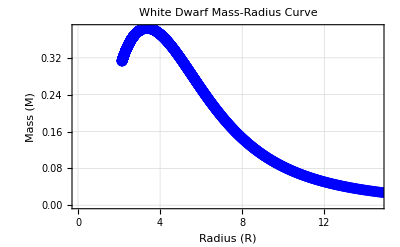

```mathematica
ClearAll[solveStar,x,y,m,fP,fRho,dfPdy];

(*1. 物理量定義*)
fP[y_]:=(1/(8 Pi^2)) (y (2 y^2/3-1) Sqrt[y^2+1]+ArcSinh[y]);
fRho[y_]:=(1/(8 Pi^2)) (y (2 y^2+1) Sqrt[y^2+1]-ArcSinh[y]);
dfPdy[y_]:=y^4/(3 Pi^2 Sqrt[y^2+1]);

(*2. 單次求解函數*)
solveStar[yc_?NumericQ]:=Module[{sol,eps=10^-6,rMax=100},sol=NDSolve[{y'[x]==-((fRho[y[x]]+fP[y[x]]) (m[x]+4 Pi x^3 fP[y[x]]))/(x (x-2 m[x]) dfPdy[y[x]]),m'[x]==4 Pi x^2 fRho[y[x]],y[eps]==yc,m[eps]==(4/3) Pi eps^3 fRho[yc],(*當動量降到接近 0 時停止計算*)WhenEvent[y[x]<10^-5,"StopIntegration"]},{y,m},{x,eps,rMax},Method->"StiffnessSwitching",PrecisionGoal->8,AccuracyGoal->8];
If[Length[sol]>0,Module[{xf,mf},xf=(y/. sol[[1]])["Domain"][[1,2]];
mf=(m/. sol[[1]])[xf];
{xf,mf}],Nothing]];

(*3. 批量計算數據*)
Print["Calculating M-R Data Points..."];
ycList=Table[yVal,{yVal,0.01,1.5,0.001}];
results=Table[Print["Computing yc = ",yv];
solveStar[yv],{yv,ycList}];

(*4. 繪製 M-R 圖*)
mrPoints=Select[results,ListQ];
If[Length[mrPoints]>0,ListLinePlot[mrPoints,Frame->True,FrameLabel->{"Radius (R)","Mass (M)"},PlotMarkers->Automatic,PlotLabel->"White Dwarf Mass-Radius Curve",PlotStyle->Blue,GridLines->Automatic],Print["No data points were generated."]]
```

正在計算高精度數據點...

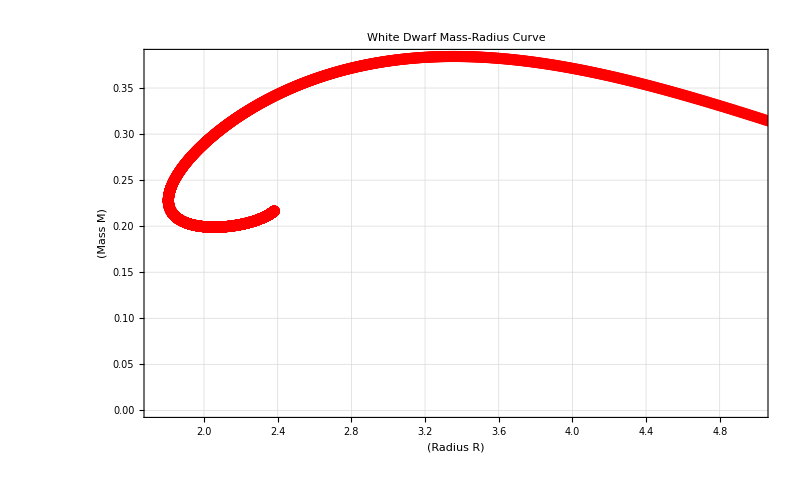

```mathematica
ClearAll[solveStar,x,y,m,fP,fRho,dfPdy];

(*1. 物理量與狀態方程定義*)
fP[y_]:=(1/(8 Pi^2)) (y (2 y^2/3-1) Sqrt[y^2+1]+ArcSinh[y]);
fRho[y_]:=(1/(8 Pi^2)) (y (2 y^2+1) Sqrt[y^2+1]-ArcSinh[y]);
dfPdy[y_]:=y^4/(3 Pi^2 Sqrt[y^2+1]);

(*2. 單次求解函數 (增加穩定性處理)*)
solveStar[yc_?NumericQ]:=Module[{sol,eps=10^-5,rMax=100},sol=NDSolve[{y'[x]==-((fRho[y[x]]+fP[y[x]]) (m[x]+4 Pi x^3 fP[y[x]]))/(x (x-2 m[x]) dfPdy[y[x]]),m'[x]==4 Pi x^2 fRho[y[x]],y[eps]==yc,m[eps]==(4/3) Pi eps^3 fRho[yc],WhenEvent[y[x]<10^-6,"StopIntegration"]},{y,m},{x,eps,rMax},Method->"StiffnessSwitching",PrecisionGoal->10,AccuracyGoal->10];
If[Length[sol]>0,Module[{xf,mf,yfunc,mfunc},yfunc=y/. sol[[1]];
mfunc=m/. sol[[1]];
xf=yfunc["Domain"][[1,2]];
mf=mfunc[xf];
{xf,mf}],Nothing]];

(*3. 增加採樣密度以獲得平滑曲線*)
Print["正在計算高精度數據點..."];
ycList=Table[yVal,{yVal,0.05,5.0,0.01}];
results=ParallelTable[solveStar[yv],{yv,ycList}]; (*使用平行計算加速*)

(*4. 繪製大尺寸圖表*)
mrPoints=Select[results,ListQ];

If[Length[mrPoints]>0,ListLinePlot[mrPoints,InterpolationOrder->3,(*使曲線平滑*)Mesh->All,MeshStyle->Directive[Red,PointSize[0.01]],Frame->True,(*設定大尺寸與字體*)ImageSize->800,BaseStyle->{FontSize->14,FontFamily->"Arial"},FrameLabel->{Style["(Radius R)",Bold,16],Style["(Mass M)",Bold,16]},PlotLabel->Style["White Dwarf Mass-Radius Curve",20,Bold],PlotStyle->{Thickness[0.003],Blue},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],FrameStyle->Thick,Background->White],Print["錯誤：未能生成有效數據點。"]]
```

NDSolve::mtdp: NDSolve`ExplicitRungeKutta[NDSolve`MethodData[5,11,{{4,3},NDSolve`EmbeddedExplicitRungeKuttaCoefficients,«6»,{False},{5,True,None}}]] does not have a correctly defined property Jacobian in NDSolve`StiffnessSwitching.

General::stop: Further output of NDSolve::mtdp will be suppressed during this calculation.

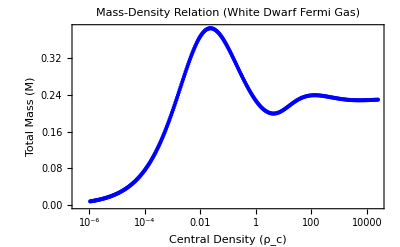

```mathematica
(*1. Physics Functions*)ClearAll[solveMassDensity,pressureFunc,densityFunc,derivP];

pressureFunc[y_]:=(1/(8 Pi^2)) (y (2 y^2/3-1) Sqrt[y^2+1]+ArcSinh[y]);
densityFunc[y_]:=(1/(8 Pi^2)) (y (2 y^2+1) Sqrt[y^2+1]-ArcSinh[y]);
derivP[y_]:=y^4/(3 Pi^2 Sqrt[y^2+1]);

(*2. Refined Solver Function*)
solveMassDensity[yc_?NumericQ]:=Module[{sol,eps=10^-5,rMax=2000,rhoC,mFinal},rhoC=densityFunc[yc];
sol=NDSolve[{y'[x]==-((densityFunc[y[x]]+pressureFunc[y[x]]) (m[x]+4 Pi x^3 pressureFunc[y[x]]))/(x (x-2 m[x]) derivP[y[x]]),m'[x]==4 Pi x^2 densityFunc[y[x]],y[eps]==yc,m[eps]==(4/3) Pi eps^3 rhoC,WhenEvent[y[x]<10^-7,"StopIntegration"]},{y,m},{x,eps,rMax},(*Fixed Method Syntax*)Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta","Automatic"}},MaxSteps->50000,PrecisionGoal->6,AccuracyGoal->6];
(*Check if NDSolve returned a valid list of rules*)If[MatchQ[sol,{{(_->_)..}..}],mFinal=(m/. sol[[1]])["ValuesOnGrid"]//Last;
{rhoC,mFinal},Nothing (*Skip if failed*)]];

(*3. Data Generation*)
(*Using a smaller sample size first to verify stability*)
yValues=Table[10^v,{v,-1.5,1.5,0.01}];
data=Map[solveMassDensity,yValues];

(*4. Visualization*)
If[Length[data]>0,ListLogLinearPlot[data,Joined->True,Mesh->All,Frame->True,GridLines->Automatic,FrameLabel->{"Central Density (ρ_c)","Total Mass (M)"},PlotLabel->"Mass-Density Relation (White Dwarf Fermi Gas)",PlotStyle->{Blue,Thick},ImageSize->Full],"Solver failed to produce valid data."]
```